```mathematica
c = .;
β = .;
α = .;
T = .;
γ = .;
f[y_] := -y*(1-y)*(c-(β*α*T*(1-γ))*(1-((1-γ)*y)));
sol = Solve[f[y]==0,y]
```

{{y→0},{y→1},{y→(-c+T α β-T α β γ)/(T α β (-1+γ)^2)}}

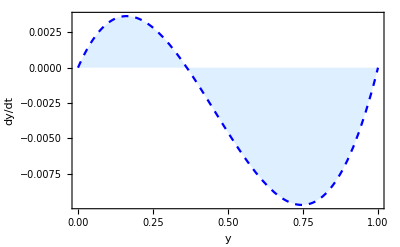

```mathematica
c = 0.1;
β = 0.55;
α = 0.3;
T = 1;
γ = 0.1;
f[y_] := -y*(1-y)*(c-(β*α*T*(1-γ))*(1-((1-γ)*y)));
Plot[ f[y],{y,0,1},PlotStyle->{Blue,Dashed},Frame->True,FrameLabel->{"y","dy/dt"},FrameStyle->Directive[Black,Thick,14],Filling->Axis,FillingStyle->LightBlue]
```

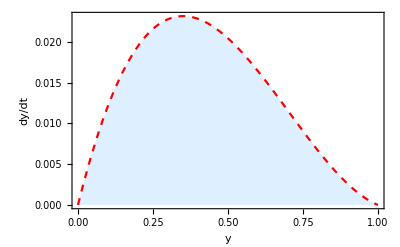

```mathematica
c = 0;
β = 0.55;
α = 0.3;
T = 1;
γ = 0.1;
f[y_] := -y*(1-y)*(c-(β*α*T*(1-γ))*(1-((1-γ)*y)));
Plot[ f[y],{y,0,1},PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{"y","dy/dt"},FrameStyle->Directive[Black,Thick,14],Filling->Axis,FillingStyle->LightBlue]
```

Piecewise[{{(-0.25+β)/β, 0.25<β<0.5}, {1. β, β≥0.5}, {0, True}}]

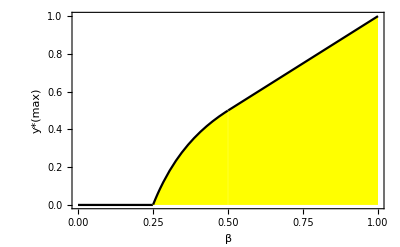

```mathematica
β=.;
c = 0.1;
α = 0.4;
T = 1;
f =(c/T);
h=Which[β≤ (f/α),0,(f/α)<β<(2*(f/α)),(1-(f/(β*α))),(2*(f/α))≤ β,((β*α)/(4*f))];
PiecewiseExpand[h]
Plot[h,{β,0,1},PlotStyle->{Black},Frame->True,FrameLabel->{"β","y*(max)"},FrameStyle->Directive[Black,Thick,14],Filling->Axis,FillingStyle->Yellow]
```

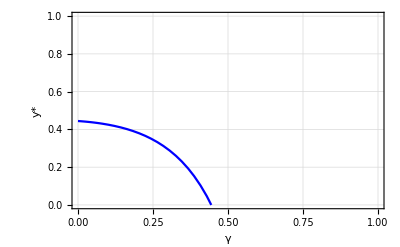

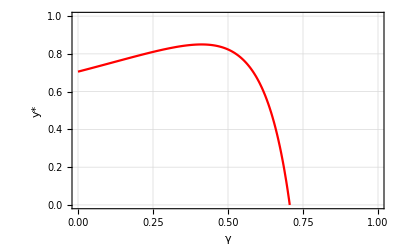

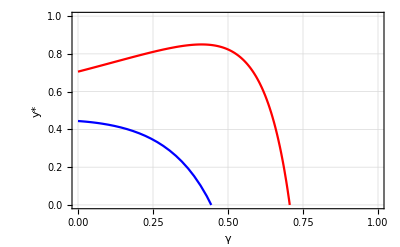

```mathematica
β=0.45;
c = 0.1;
α = 0.4;
T = 1;
γ = 0.1;
μ = 0.2;
f =(c/T);
z = (1-γ);
i[γ_]:= ((1/(1-γ))*(1-(c/(β*T*α*(1-γ)))))
a = Plot[ i[γ],{γ,0,1}, PlotRange-> {0,1},PlotStyle->{Blue},Axes->False,AxesOrigin->{-0,0},Frame->True,FrameLabel->{"γ","y*"},FrameStyle->Directive[Black,Thick,14],GridLines->Automatic,PlotLegends->"Expressions"]
β=0.85;
c = 0.1;
α = 0.4;
T = 1;
γ = 0.1;
μ = 0.2;
f =(c/T);
z = (1-γ);
i[γ_]:= ((1/(1-γ))*(1-(c/(β*T*α*(1-γ)))))
b =Plot[ i[γ],{γ,0,1}, PlotRange-> {0,1},PlotStyle->{Red},Axes->False,AxesOrigin->{-0,0},Frame->True,FrameLabel->{"γ","y*"},FrameStyle->Directive[Black,Thick,14],GridLines->Automatic,PlotLegends->"Expressions"]
Show[a,b]
```

```mathematica
β=.;
c = 0.1;
α = .;
T = 1;
γ = 0.1;
μ = 0.2;
f =(c/T);
z = (1-γ);
i[α_,β_]:= ((1/(1-γ))*(1-(c/(β*T*α*(1-γ)))))
plot1 = DensityPlot[i[α,β],{α,0,1},{β,0,1},ColorFunction -> "Rainbow", PlotPoints ->40,Axes->False,AxesOrigin->{-0,0},Frame->True,FrameLabel->{"β","α"},FrameStyle->Directive[Black,Thick,14]];
plot2 = ContourPlot[i[α,β] == 0, {α,0,1}, {β,0,1}, 
   ContourStyle -> {Thick, White}, PlotPoints -> 40];
Show[plot1,plot2]
```

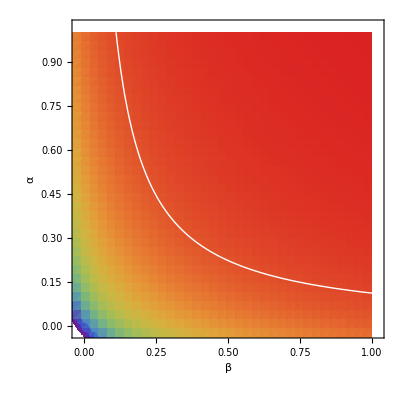

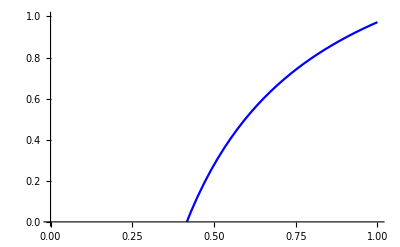

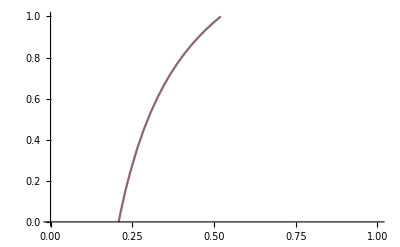

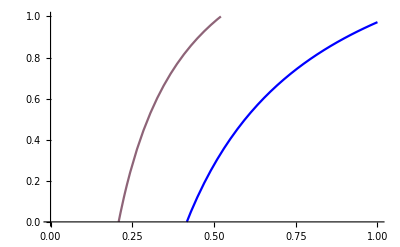

```mathematica
β=.;
c = 0.1;
α = 0.4;
T = 1;
γ = 0.4;
μ = 0.1;
f =(c/T);
z = (1-γ);
r = 1;
k =0;
i[β_]:= ((1/(1-γ))*(1-(c/(β*T*α*(1-γ)))));
a1 =Plot[i[β],{β,0,1},PlotRange->{0,1},PlotStyle->{Blue}]
β=.;
c = 0.05;
α = 0.4;
T = 1;
γ = 0.4;
μ = 0.1;
f =(c/T);
z = (1-γ);
r = 1;
k =0;
i[β_]:= ((1/(1-γ))*(1-(c/(β*T*α*(1-γ)))));
a2 = Plot[i[β],{β,0,1},PlotRange->{0,1},ColorFunction -> "Rainbow"]
Show[a1,a2]
```